First generate a single file with a list of all individual data, e.g. via:

ls -1 Data/PseudoSpectraEnergyNorm_N_100_* > list_of_files.txt

or

ls Data/ | grep ‘PseudoSpectraEnergyNorm_N_100’ > list_of_files.txt

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];

Prec=500;
Nz=450;
FuncName="Cos";
spin=-2;
l=2;

kmin=2;
kmax=30;
δk=2;
Nk=(kmax-kmin)/δk;
nk=Nk+1;

ymin=-15;
ymax=-1;
δy=1/2;
Ny=(ymax-ymin)/δy;
ny=Ny+1;

k=Range[kmin,kmax,δk];
y=Range[ymin,ymax,δy];

nTotal=ny*nk
ik=0;
iy=0;


QNMAxial=Table[,{ik,1,nk},{iy,1,ny}];
QNMPolar=Table[,{ik,1,nk},{iy,1,ny}];

For[ik=1,ik≤nk,ik++,

For[iy=1,iy≤ny,iy++,



fnAxial="Data/AxialParity/Spectra"<>FuncName<>"_N_"<>ToString[Nz]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

fnPolar="Data/PolarParity/Spectra"<>FuncName<>"_N_"<>ToString[Nz]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";


frAxial=Import[fnAxial,"Table"];
QNMAxial[[ik,iy]]=Import[fnAxial,"Table"];
frPolar=Import[fnPolar,"Table"];
QNMPolar[[ik,iy]]=Import[fnPolar,"Table"];
]
]
```

435

### Select data at a given k

```mathematica
kread=10;
Ik=Position[k,kread][[1,1]];
nQNM=78; (*Number of considered QNMs*)
QNMAxialFIXEDk=Table[Take[Reverse[QNMAxial[[Ik, iy]]], nQNM],{iy,1,ny}];
QNMPolarFIXEDk=Table[Take[Reverse[QNMPolar[[Ik, iy]]],nQNM],{iy,1,ny}];
```

```mathematica
PlotTable=Table[ListPlot[{QNMAxialFIXEDk[[iy]],QNMPolarFIXEDk[[iy]]},
PlotLabel->"k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{-50,0},{-30,30}},
PlotLegends->{"Axial", "Polar"},

ImageSize->Large
],{iy,1,ny}];
```

```mathematica
ListAnimate[PlotTable]
```

### Select data at a given ϵ

25

Part::partw: Part 30 of {-15,-29/2,-14,-27/2,-13,-25/2,-12,-23/2,-11,-21/2,«19»} does not exist.

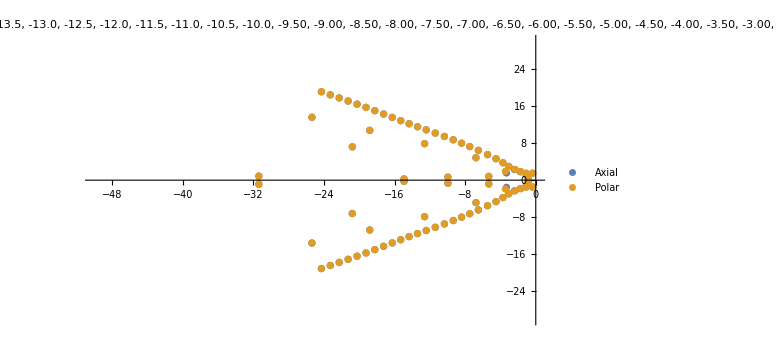

```mathematica
yread=-3;
Iy=Position[y,yread][[1,1]]
QNMAxialFIXEDky=QNMAxialFIXEDk[[Iy]];
QNMPolarFIXEDky=QNMPolarFIXEDk[[Iy]];
ListPlot[{QNMAxialFIXEDky,QNMPolarFIXEDky},
PlotLabel->"k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[Iy]],3]],
PlotRange->{{-50,0},{-30,30}},
PlotLegends->{"Axial", "Polar"},

ImageSize->Large
]
```

#### Check convergence

```mathematica
NzCHECK=500;
QNMAxialCHECK=Table[,{iy,1,ny}];
QNMPolarCHECK=Table[,{iy,1,ny}];

For[iy=1,iy≤ny,iy++,


fnAxial="Data/AxialParity/Spectra"<>FuncName<>"_N_"<>ToString[NzCHECK]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[Ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

fnPolar="Data/PolarParity/Spectra"<>FuncName<>"_N_"<>ToString[NzCHECK]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[Ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";


fload=Import[fnAxial,"Table"];
QNMAxialCHECK[[iy]]=Take[Reverse[fload], nQNM];
fload=Import[fnPolar,"Table"];
QNMPolarCHECK[[iy]]=Take[Reverse[fload], nQNM];
]
```

```mathematica
ΔAxialConvergence=Abs[QNMAxialCHECK-QNMAxialFIXEDk];
ΔPolarConvergence=Abs[QNMPolarCHECK-QNMPolarFIXEDk];
```

```mathematica
PlotComparisionAxial=Table[ListPlot[{QNMAxialCHECK[[iy]],QNMAxialFIXEDk[[iy]]},
PlotLabel->"(AXIAL) k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{-25,0},{-15,15}},
PlotLegends->{"NzCHECK="<>ToString[NzCHECK],"Nz="<>ToString[Nz]},
ImageSize->Large,
PlotMarkers->"OpenMarkers"
],{iy,1,ny}];
PlotComparisionPolar=Table[ListPlot[{QNMPolarCHECK[[iy]],QNMPolarFIXEDk[[iy]]},
PlotLabel->"(POLAR) k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{-25,0},{-15,15}},
PlotLegends->{"NzCHECK="<>ToString[NzCHECK],"Nz="<>ToString[Nz]},
ImageSize->Large,
PlotMarkers->"OpenMarkers"
],{iy,1,ny}];
ListAnimate[PlotComparisionAxial]
ListAnimate[PlotComparisionPolar]
```

```mathematica
PlotConvergence=Table[ListLogLogPlot[{ΔAxialConvergence[[iy]],ΔPolarConvergence[[iy]]},
PlotLabel->"k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{10^(-19),10^3},{10^(-19),10^3}},
PlotLegends->{"Axial", "Polar"},
ImageSize->Large
],{iy,1,ny}];
ListAnimate[PlotConvergence]
```

#### Check convergence

```mathematica
NzCHECK=500;
QNMAxialCHECK=Table[,{iy,1,ny}];
QNMPolarCHECK=Table[,{iy,1,ny}];

For[iy=1,iy≤ny,iy++,


fnAxial="Data/AxialParity/Spectra"<>FuncName<>"_N_"<>ToString[NzCHECK]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[Ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

fnPolar="Data/PolarParity/Spectra"<>FuncName<>"_N_"<>ToString[NzCHECK]<>"_spin"<>ToString[spin]<>"_l"<>ToString[l]<>"_Freq_log10eps_"<>ToString[N[y[[iy]]]]<>"_ksig_"<>ToString[k[[Ik]]]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";


fload=Import[fnAxial,"Table"];
QNMAxialCHECK[[iy]]=Take[Reverse[fload], nQNM];
fload=Import[fnPolar,"Table"];
QNMPolarCHECK[[iy]]=Take[Reverse[fload], nQNM];
]
```

```mathematica
ΔAxialConvergence=Abs[QNMAxialCHECK-QNMAxialFIXEDk];
ΔPolarConvergence=Abs[QNMPolarCHECK-QNMPolarFIXEDk];
```

```mathematica
PlotComparisionAxial=Table[ListPlot[{QNMAxialCHECK[[iy]],QNMAxialFIXEDk[[iy]]},
PlotLabel->"(AXIAL) k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{-25,0},{-15,15}},
PlotLegends->{"NzCHECK="<>ToString[NzCHECK],"Nz="<>ToString[Nz]},
ImageSize->Large,
PlotMarkers->"OpenMarkers"
],{iy,1,ny}];
PlotComparisionPolar=Table[ListPlot[{QNMPolarCHECK[[iy]],QNMPolarFIXEDk[[iy]]},
PlotLabel->"(POLAR) k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{-25,0},{-15,15}},
PlotLegends->{"NzCHECK="<>ToString[NzCHECK],"Nz="<>ToString[Nz]},
ImageSize->Large,
PlotMarkers->"OpenMarkers"
],{iy,1,ny}];
ListAnimate[PlotComparisionAxial]
ListAnimate[PlotComparisionPolar]
```

```mathematica
PlotConvergence=Table[ListLogLogPlot[{ΔAxialConvergence[[iy]],ΔPolarConvergence[[iy]]},
PlotLabel->"k="<>ToString[kread]<>", ϵ = 10^"<>ToString[N[y[[iy]],3]],
PlotRange->{{10^(-19),10^3},{10^(-19),10^3}},
PlotLegends->{"Axial", "Polar"},
ImageSize->Large
],{iy,1,ny}];
ListAnimate[PlotConvergence]
```